```mathematica
f[x_] :=(x^5-2 x^2+3x+4)/(x^5-2x-1)
```

```mathematica
f[1]
```

-3

```mathematica
f[2]
```

34/27

```mathematica
f[3]
```

119/118

```mathematica
f[4]
```

144/145

```mathematica
ClearAll[f]
```

```mathematica
(x^5-2 x^2+3x+4)/(x^5-2x-1) /. {{x-> 1}, {x -> 2}, {x -> 3}, {x -> 4}}
```

{-3,34/27,119/118,144/145}

```mathematica
Table[g[i], {i, 1, 12}]
```

{g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12]}

```mathematica
sez= {10,20,30,40,50,60,70}
```

{10,20,30,40,50,60,70}

```mathematica
Take[sez, 3]
```

{10,20,30}

```mathematica
Take[sez,-2]
```

{60,70}

```mathematica
Take[sez,{2,4}]
```

{20,30,40}

```mathematica
sez[[{2,3,5}]]
```

{20,30,50}

```mathematica
Drop[sez,{4,5}]
```

{10,20,30,60,70}

```mathematica
sez = {x^3,x^2,a}
```

{x^3,x^2,a}

```mathematica
sez /. {{x -> 3},{x -> x^2},{x^2 -> x},{x -> {1, 2, 3}},{x -> 2, a-> 3}}
```

{{27,9,a},{x^6,x^4,a},{x^3,x,a},{{1,8,27},{1,4,9},a},{8,4,3}}

```mathematica
Table[sez /. {x -> i}, {i, 1, 3}]

D[x^5+4 x^3−9, x] /. {{x -> 1}, {x -> 5}}
```

{{1,1,a},{8,4,a},{27,9,a}}

{17,3425}

```mathematica
D[e^(x^(1/4)), x] /. {{x -> 1}, {x -> 2}}
```

{1/4 e Log[e],(e^(2^(1/4)) Log[e])/(4 2^(3/4))}

```mathematica
D[RealAbs[x+1]] /. {{x -> 1}, {x -> -1}}
```

{2,0}

```mathematica
f[x_]:=ax^2 3b
```

```mathematica
ClearAll[a, b, x]
```

```mathematica
f'[x] /. {{x -> 1}, {x -> 2}}
```

{0,0}

```mathematica
{0,0}
```

```mathematica
{0,0}
```

{0,0}

```mathematica
ClearAll[f]
```

```mathematica
Definition[f]
```

Null

```mathematica
f[x_]:= x^3 Log[4x+5]
```

```mathematica
Definition[f]
```

f[x_]:=x^3 Log[4 x+5]

f[x_]:=x^3 In[4 x+5]

f[x_]:=x^3 In[4 x+5]

f[x_]:=x^3 ln[4 x+5]

f[x_]:=x^3 In[4 x+5]

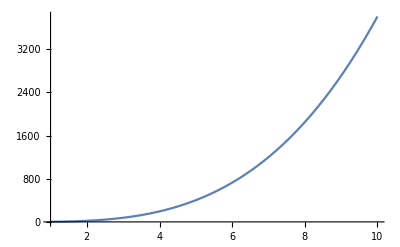

```mathematica
Plot[f[x], {x, 1, 10}]
```

```mathematica
f[5] //N
```

402.359

```mathematica
f'[x]
```

(4 x^3)/(5+4 x)+3 x^2 Log[5+4 x]

```mathematica
D[x^3 Log[4x+5], x]
```

CoefficientD[x^3 Log[5+4 x],x]

Global`f